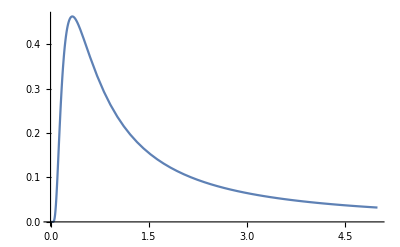

```mathematica
Plot[PDF[InverseGammaDistribution[0.5,0.5],x],{x,0,5}]
```

```mathematica
Expectation[z,z\[Distributed] TransformedDistribution[x*y,{x\[Distributed] InverseGammaDistribution[0.5,0.5],y\[Distributed] InverseGammaDistribution[10.0,10.0]}]]
```

-1.11111

```mathematica
Integrate[x*PDF[GammaDistribution[a,1/z],x],{x,lower,∞},Assumptions-> {lower>0,z>0,a>0}]
```

Gamma[1+a,lower z]/(z Gamma[a])

```mathematica
Integrate[x^2*PDF[GammaDistribution[a,1/z],x],{x,lower,∞},Assumptions-> {lower>0,z>0,a>0}]
```

Gamma[2+a,lower z]/(z^2 Gamma[a])

```mathematica
Gamma
```